```mathematica
Q[x_]:=1/2 Erfc[x/Sqrt[2]]
```

```mathematica
h * Q[η-μ]+f Q[η]
```

1/2 f Erfc[η/(√2)]+1/2 h Erfc[(η-μ)/(√2)]

```mathematica
Manipulate[Plot[h * Q[η-μ]+f Q[η]-μ,{μ,0,10},PlotRange->{Automatic,{0,Automatic}},AxesLabel->Automatic],{{h,2.98},0,10},{{f,-1},-10,0},{{η,0},-2,2}]
```

```mathematica
Manipulate[Plot[h * Q[η-μ]+f Q[η]-μ,{η,-4,2},PlotRange->{Automatic,{0,Automatic}},AxesLabel->Automatic],{{h,2.98},0,10},{{f,-1},-10,0},{μ,0,10}]
```

```mathematica
Manipulate[Plot[α * Q[γ]+γ,{γ,-4,4},PlotRange->{Automatic,Automatic},AxesLabel->Automatic],{{α,.01},0,50}]
```

```mathematica
Manipulate[Plot3D[{h * Q[η-μ]+f Q[η]+μ,f Q[η],h * Q[η-μ]},{η,-10,10},{μ,0,10},PlotLegends->{"total cost", "neg false alarm", "amp hit rate"},AxesLabel->Automatic],{{f, -8.6},-20,-.001},{{h, 8.6},.001,20}]
```

```mathematica
Minimize[h * Q[η-μ]+f Q[η]+μ,μ]
```

```mathematica
Minimize[μ+1/2 f Erfc[η/(√2)]+1/2 h Erfc[(η-μ)/(√2)],μ]
```

Minimize[μ+1/2 f Erfc[η/(√2)]+1/2 h Erfc[(η-μ)/(√2)],μ]

```mathematica
NMinimize[μ+1/2 -1 Erfc[η/(√2)]+1/2 1 Erfc[(η-μ)/(√2)],{μ, η}]
```

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{-1.81665×10^128,{μ→-1.81665×10^128,η→-1.04734×10^23}}

```mathematica
Plot3D[{Abs[μ]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-Abs[μ]}/.{h-> htmp, f-> ftmp},{η,μ}][[2]]}},{h,0,5},{f,-10,0},PlotLegends->{Automatic},AxesLabel->Automatic, PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[{Q[η]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-Abs[μ]}/.{h-> htmp, f-> ftmp},{η,μ}][[2]]}},{h,0,5},{f,-5,-10},PlotLegends->{Automatic},AxesLabel->Automatic, PlotRange->All]
```

-Graphics3D-

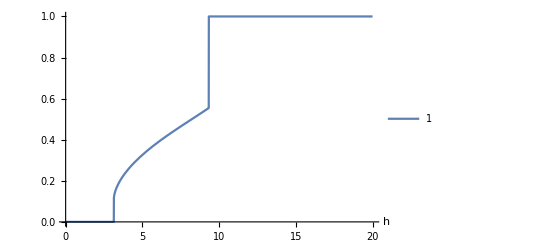

```mathematica
Plot[{Q[η]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-μ^2}/.{ f-> -5},{η,μ}][[2]]}},{h,0,20},PlotLegends->{Automatic},AxesLabel->Automatic, PlotRange->All]
```

```mathematica
Manipulate[Plot[{Q[η-Abs[μ]]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-μ^2}/.{f-> ftmp},{η,μ}][[2]]}},{h,0,20},PlotLegends->{Automatic},AxesLabel->Automatic, PlotRange->All],{{ftmp,-5},-10,0}]
```

NMaximize::nnum: The function value 0.513471-0.179147 ftmp is not a number at {η,μ} = {0.918621,0.716689}.

ReplaceAll::reps: {η,μ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMaximize::nnum: The function value 0.342049-0.179147 ftmp is not a number at {η,μ} = {0.918621,0.716689}.

ReplaceAll::reps: {η,μ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NMaximize::nnum: The function value 0.170626-0.179147 ftmp is not a number at {η,μ} = {0.918621,0.716689}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{Q[η-Abs[μ]]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-μ^2}/.{f-> ftmp},{η,μ}][[2]]},Q[η]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-μ^2}/.{ f-> ftmp},{η,μ}][[2]]}},{h,0,20},PlotLegends->{"Hit","FA"},AxesLabel->Automatic, PlotRange->All],{{ftmp,-5},-10,0}]
```

```mathematica
Manipulate[Plot[{μ^2/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-μ^2}/.{f-> ftmp},{η,μ}][[2]]},Q[η-Abs[μ]]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-μ^2}/.{f-> ftmp},{η,μ}][[2]]},Q[η]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-μ^2}/.{ f-> ftmp},{η,μ}][[2]]}},{h,0,15},PlotLegends->{"mean squred","Hit","FA"},AxesLabel->Automatic, PlotRange->All],{{ftmp,-5},-10,0}]
```

```mathematica
Manipulate[Plot[{Abs[μ]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-μ^2}/.{f-> ftmp},{η,μ}][[2]]}},{h,0,20},PlotLegends->{Automatic},AxesLabel->Automatic, PlotRange->All],{{ftmp,-5},-10,0}]
```

```mathematica
Manipulate[Plot[{η/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-μ^2}/.{f-> ftmp},{η,μ}][[2]]}},{h,3.2,9.3},PlotLegends->{Automatic},AxesLabel->Automatic, PlotRange->All],{{ftmp,-5},-10,0}]
```

```mathematica
LogisticSigmoid[Abs[μ]]
```

```mathematica
Manipulate[Plot[{μ^2/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-μ^2}/.{f-> ftmp},{η,μ}][[2]]},Q[η-Abs[μ]]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-μ^2}/.{f-> ftmp},{η,μ}][[2]]},Q[η]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-μ^2}/.{ f-> ftmp},{η,μ}][[2]]}},{h,0,15},PlotLegends->{"mean squred","Hit","FA"},AxesLabel->Automatic, PlotRange->All],{{ftmp,-5},-10,0}]
```

```mathematica
Manipulate[Plot[{Q[η-Abs[μ]]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-10*(LogisticSigmoid[Abs[μ]/1] - 0.5)}/.{f-> ftmp},{η,μ}][[2]]},Q[η]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-10*(LogisticSigmoid[Abs[μ]/1] - 0.5)}/.{ f-> ftmp},{η,μ}][[2]]}},{h,0,12},PlotLegends->{"Hit","FA"},AxesLabel->Automatic, PlotRange->All],{{ftmp,-5},-10,0}]
```

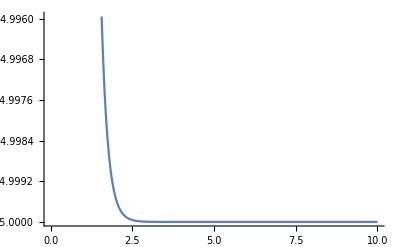

```mathematica
Plot[-10*(LogisticSigmoid[Abs[μ]/5] - 0.5),{μ,0,10}]
```

```mathematica
Manipulate[Plot[{Q[η-Abs[μ]]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-Abs[μ]^3}/.{f-> ftmp},{η,μ}][[2]]},Q[η]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-Abs[μ]^3}/.{ f-> ftmp},{η,μ}][[2]]}},{h,0,20},PlotLegends->{"Hit","FA"},AxesLabel->Automatic, PlotRange->All],{{ftmp,-5},-10,0}]
```

```mathematica
Manipulate[Plot[{Q[η-Abs[μ]]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-Abs[μ]^3}/.{f-> ftmp},{η,μ}][[2]]},Q[η]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-Abs[μ]^3}/.{ f-> ftmp},{η,μ}][[2]]}},{h,0,20},PlotLegends->{"Hit","FA"},AxesLabel->Automatic, PlotRange->All],{{ftmp,-5},-10,0}]
```

```mathematica
Manipulate[Plot[{Q[η-Abs[μ]]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-Abs[μ]^(1/2)}/.{f-> ftmp},{η,μ}][[2]]},Q[η]/.{NMaximize[{h * Q[η-Abs[μ]]+f Q[η]-Abs[μ]^(1/2)}/.{ f-> ftmp},{η,μ}][[2]]}},{h,0,20},PlotLegends->{"Hit","FA"},AxesLabel->Automatic, PlotRange->All],{{ftmp,-5},-10,0}]
```

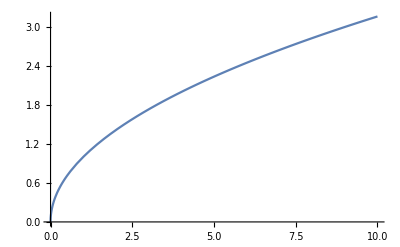

```mathematica
Plot[x^(1/2),{x,0,10},PlotRange->All]
```

```mathematica
η->ConditionalExpression[-(-μ^2-2 Log[-f/h])/(2 μ), f<0&&h>0]
```

```mathematica
Solve[μ^2+2 Log[-f/h]-2 μ η ==0,μ]
```

{{μ→η-√(η^2-2 Log[-f/h])},{μ→η+√(η^2-2 Log[-f/h])}}

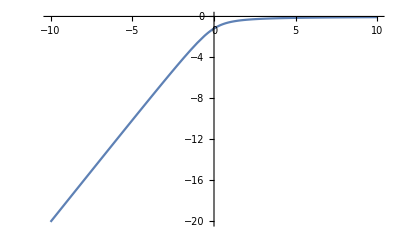

```mathematica
Plot[η-√(η^2-2 Log[1/2]),{η,-10,10}]
```

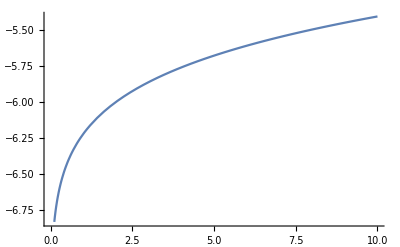

```mathematica
Plot[k-√(k^2-2 Log[f/2])/.{k-> -3},{f,0,10}]
```

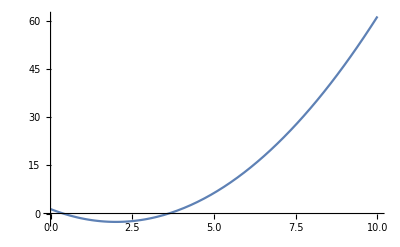

```mathematica
Plot[μ^2+2 Log[2]-2 μ k /.{k-> 2},{μ,0,10}]
```

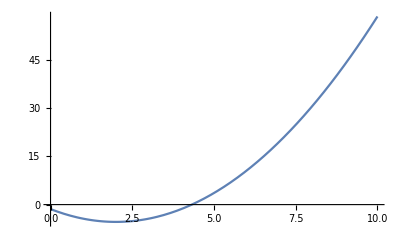

```mathematica
Plot[μ^2+2 Log[1/2]-2 μ η /.{η-> 2},{μ,0,10}]
```